```mathematica
(* Broadband pulses with fixed profile bandwidths ϵ = 0.2, 0.3, 0.4, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/3 *)
(* Error < 10^-2 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.01;
error=", error="<>ToString@err;
totalArea[rule_,sym_]:=Module[
{vars=rule/.Rule[a_,b_]->a},
area=Total[Abs[vars[[Length[vars]/2+1;;-1]]/.rule]];
If[sym,area=2area-vars[[-1]]/.rule];
area]
```

BB3; p=1, error=0.01

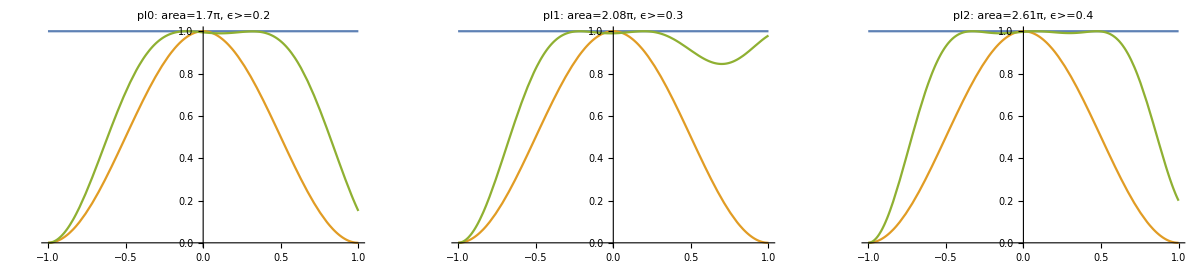

BB3; p=1/2, error=0.01

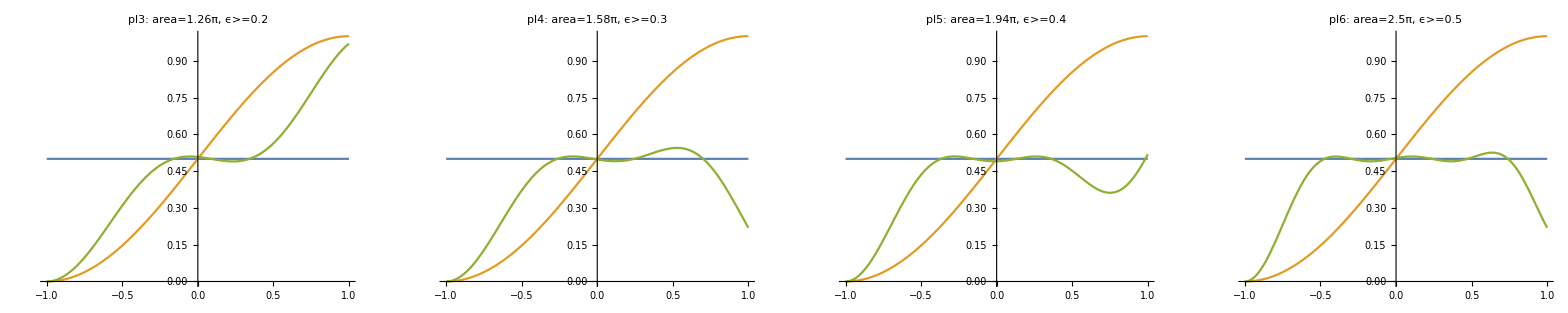

BB3; p=1/3, error=0.01

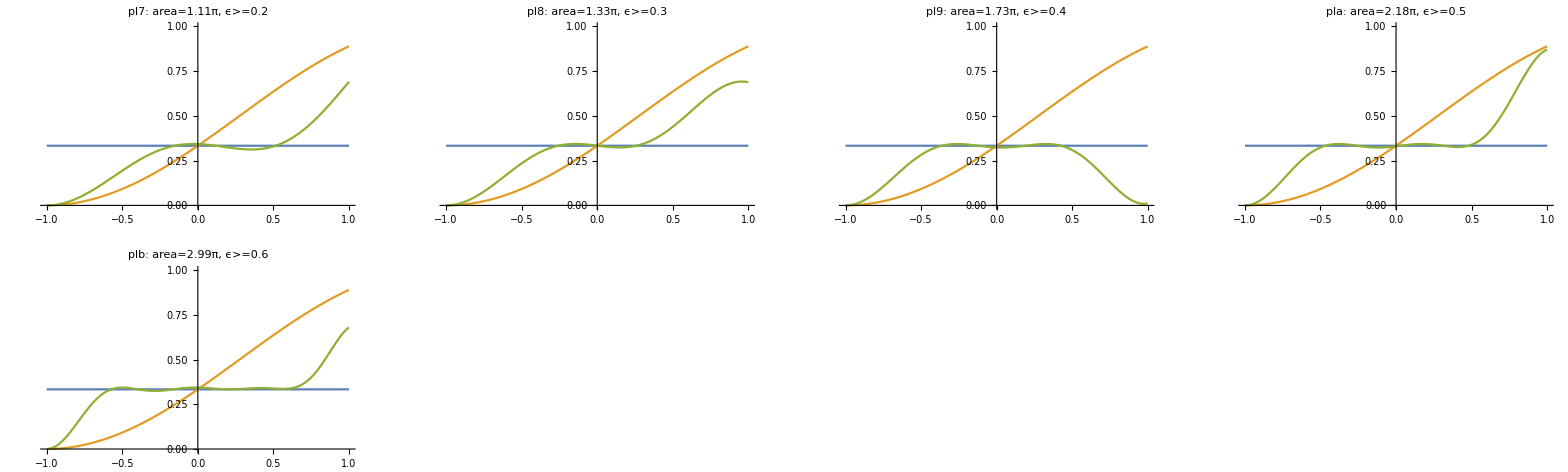

```mathematica
(*N=3*)
sequence=U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl0=plt[1,{Δ1->-0.7673,Δ2->0.7370,Δ3->10^-10,Ω1->0.8356,Ω2->0.8663,Ω3->0.},"pl0"];
pl1=plt[1,{Δ1->-0.7380,Δ2->0.0264,Δ3->0.7437,Ω1->0.5825,Ω2->0.9426,Ω3->0.5592},"pl1"];
pl2=plt[1,{Δ1->0.8352,Δ2->0.0082,Δ3->-0.8162,Ω1->0.6332,Ω2->1.3268,Ω3->0.6457},"pl2"];

pl3=plt[1/2,{Δ1 ->0.1391, Δ2 ->-0.1568, Δ3 ->0.9610, Ω1 ->0.1323, Ω2 ->0.4274, Ω3 ->0.7043},"pl3"];
pl4=plt[1/2,{Δ1->0.3529,Δ2->0.2589,Δ3->0.5840,Ω1->1.1561,Ω2->0.0513,Ω3->0.3694},"pl4"];
pl5=plt[1/2,{Δ1->0.1076,Δ2->0.3901,Δ3->0.9057,Ω1->0.7010,Ω2->0.7992,Ω3->0.4440},"pl5"];
pl6=plt[1/2,{Δ1->0.9462,Δ2->0.553,Δ3->0.158,Ω1->0.4275,Ω2->0.9924000000000001,Ω3->1.0816},"pl6"];

pl7=plt[1/3,{Δ1 -> 0.1828, Δ2 -> 0.2984, Δ3 -> 0.5613, Ω1 -> 0.6058, Ω2 -> 0.1345, Ω3 -> 0.3730},"pl7"];
pl8=plt[1/3,{Δ1 -> 0.0767, Δ2 -> 0.3189, Δ3 -> 0.8578, Ω1 -> 0.0856, Ω2 -> 0.7382, Ω3 -> 0.5105},"pl8"];
pl9=plt[1/3,{Δ1 -> 1.0170, Δ2 -> 0.0342, Δ3 -> 0.4313, Ω1 -> 0.6263, Ω2 -> 0.5028, Ω3 -> 0.5971},"pl9"];
pla=plt[1/3,{Δ1 -> 0.0254, Δ2 -> -0.6538, Δ3 -> -0.9490, Ω1 -> 0.2923, Ω2 -> 1.3963, Ω3 -> 0.4891},"pla"];
plb=plt[1/3,{Δ1 -> 0.4934, Δ2 -> 0.6461, Δ3 -> 0.9730, Ω1 -> 1.6500, Ω2 -> 0.9498, Ω3 -> 0.3943},"plb"];

GGrid[Text[Style["BB3; p=1"<> error,FontSize->20]],{{pl0,pl1,pl2,Null}},ImageSize->Full]
GGrid[Text[Style["BB3; p=1/2"<> error,FontSize->20]],{{pl3,pl4,pl5,pl6}},ImageSize->Full]
GGrid[Text[Style["BB3; p=1/3"<> error,FontSize->20]],{{pl7,pl8,pl9,pla},{plb}},ImageSize->Full]
```

BB4; p=1, error=0.01

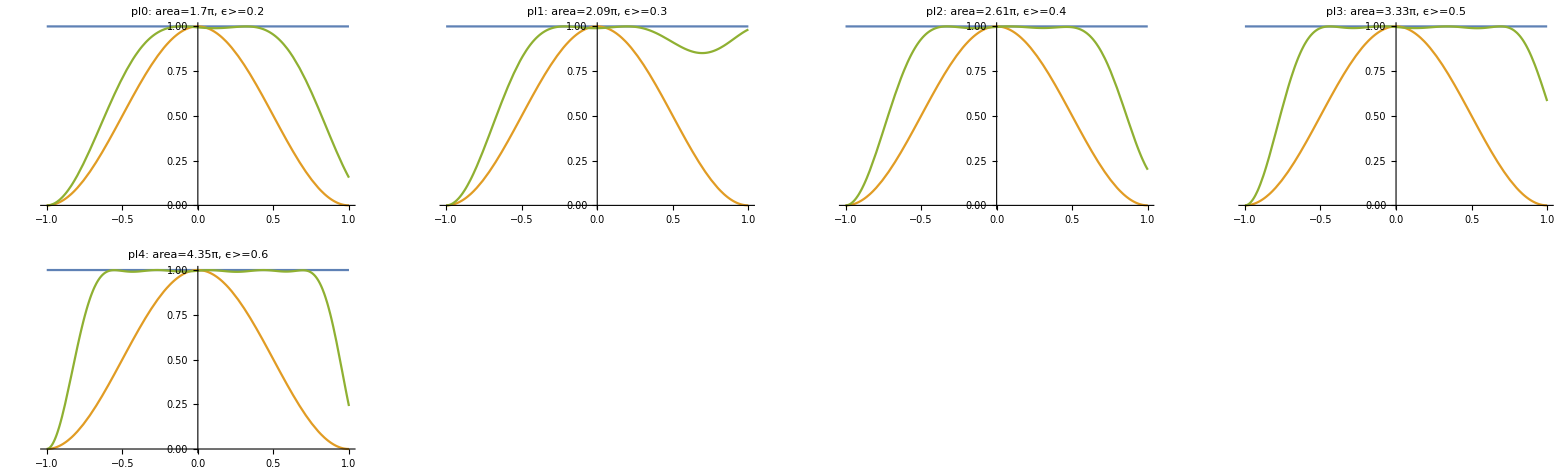

BB4; p=1/2, error=0.01

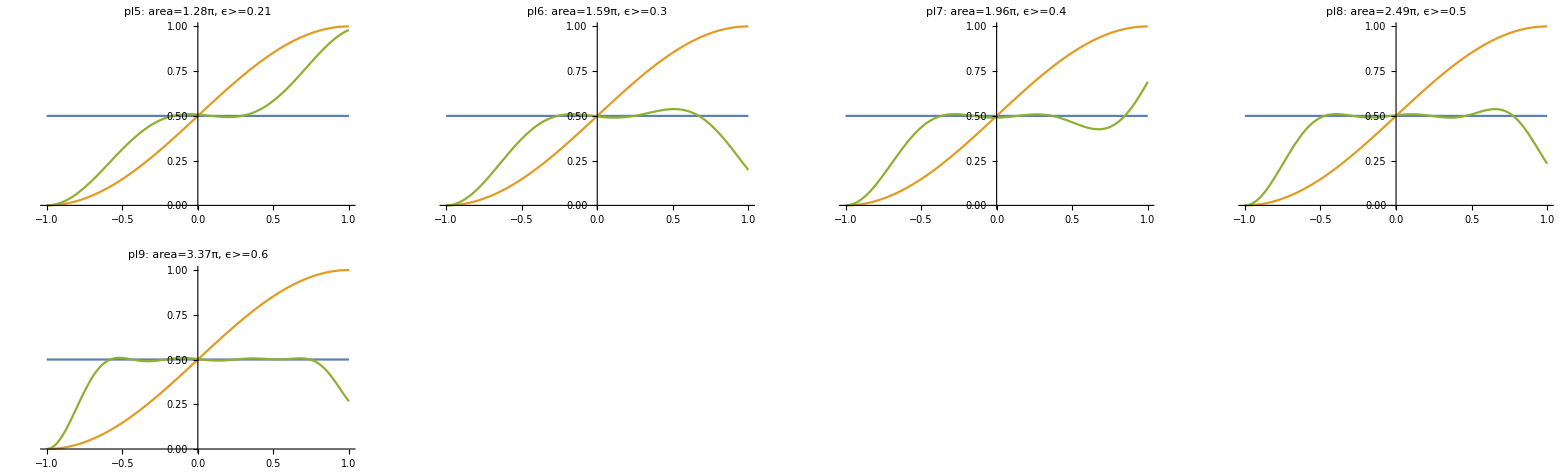

BB4; p=1/3, error=0.01

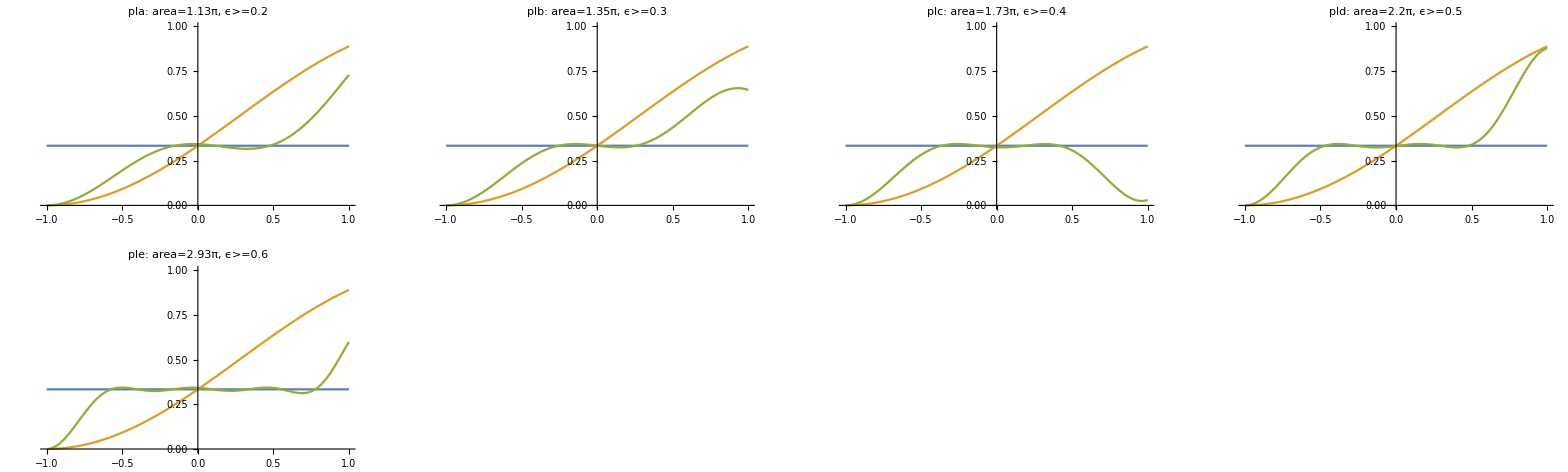

```mathematica
(*N=4*)
sequence=U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl0=plt[1,{Δ1->-0.6975,Δ2->0.0606,Δ3->0.1813,Δ4->0.4048,Ω1->0.7346,Ω2->0.3928,Ω3->0.0492,Ω4->0.5239},"pl0"];
pl1=plt[1,{Δ1->-0.1939,Δ2->-0.4613,Δ3->-0.0316,Δ4->0.7442,Ω1->0.2505,Ω2->0.2436,Ω3->1.0028,Ω4->0.5918},"pl1"];
pl2=plt[1,{Δ1->1.1841,Δ2->-0.8329,Δ3->-0.0321,Δ4->0.8222,Ω1->0.0013,Ω2->0.6151,Ω3->1.3301,Ω4->0.6605},"pl2"];
pl3=plt[1,{Δ1->0.8347,Δ2->0.2665,Δ3->-0.2868,Δ4->-0.8451,Ω1->0.5253,Ω2->1.1388,Ω3->1.1449,Ω4->0.5201},"pl3"];
pl4=plt[1,{Δ1->1.0404,Δ2->-0.7422,Δ3->0.6674,Δ4->-1.0624,Ω1->1.5974,Ω2->0.5363,Ω3->0.7633,Ω4->1.4500},"pl4"];

pl5=plt[1/2,{Δ1 ->0.3476, Δ2 -> 0.4567, Δ3 -> 0.1576, Δ4 -> -0.0902, Ω1 -> 0.2302, Ω2 -> 0.3330, Ω3 -> 0.1830, Ω4 -> 0.5347},"pl5"];
pl6=plt[1/2,{Δ1 ->0.6459, Δ2 ->0.4074,Δ3 -> -0.2016, Δ4 -> 0.3507, Ω1 -> 0.4085, Ω2 -> 0.0259, Ω3 -> 0.0219, Ω4 -> 1.1370},"pl6"];
pl7=plt[1/2,{Δ1 -> 0.0739, Δ2 -> 1.0570,  Δ3 -> -0.0544, Δ4 -> -0.6939,  Ω1 -> 0.0244, Ω2 -> 1.1807, Ω3 -> 0.2833, Ω4 -> 0.4695},"pl7"];
pl8=plt[1/2,{Δ1->0.1543,Δ2->0.5585,Δ3->0.4380,Δ4->0.4733,Ω1->1.0677,Ω2->1.0067,Ω3->0.1788,Ω4->0.2329},"pl8"];
pl9=plt[1/2,{Δ1 -> 0.0963, Δ2 -> 0.3205, Δ3 -> 0.6542, Δ4 -> 0.9736, Ω1 -> 1.0700, Ω2 -> 1.0321, Ω3 -> 0.8971, Ω4 -> 0.3704},"pl9"];

pla=plt[1/3,{Δ1->-0.1113,Δ2->0.4888,Δ3->0.1215,Δ4->0.4536,Ω1->0.3877,Ω2->0.3810,Ω3->0.0827,Ω4->0.2741},"pla"];
plb=plt[1/3,{Δ1->0.1255,Δ2->0.4080,Δ3->0.2561,Δ4->0.4721,Ω1->0.0676,Ω2->0.9087,Ω3->0.0109,Ω4->0.3635},"plb"];
plc=plt[1/3,{Δ1->1.0017,Δ2->0.0609,Δ3->0.1539,Δ4->0.2515,Ω1->0.5812,Ω2->0.4518,Ω3->0.2092,Ω4->0.4906},"plc"];
pld=plt[1/3,{Δ1->0.3782,Δ2->-0.2393,Δ3->0.7014,Δ4->0.9488,Ω1->0.1075,Ω2->0.0878,Ω3->1.5136,Ω4->0.4943},"pld"];
ple=plt[1/3,{Δ1->0.1536,Δ2->0.4530,Δ3->0.6118,Δ4->0.9508,Ω1->0.0383,Ω2->1.5509,Ω3->0.9411,Ω4->0.4023},"ple"];

GGrid[Text[Style["BB4; p=1"<> error,FontSize->20]],{{pl0,pl1,pl2,pl3},{pl4}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8},{pl9}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/3"<> error,FontSize->20]],{{pla,plb,plc,pld},{ple}},ImageSize->Full]
```

BB5 p=1, error=0.01

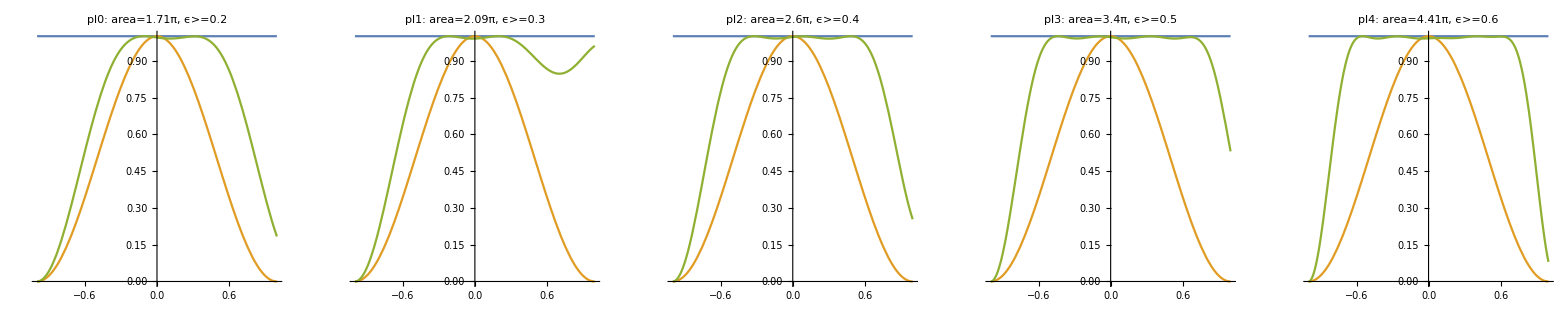

BB5 p=1/2, error=0.01

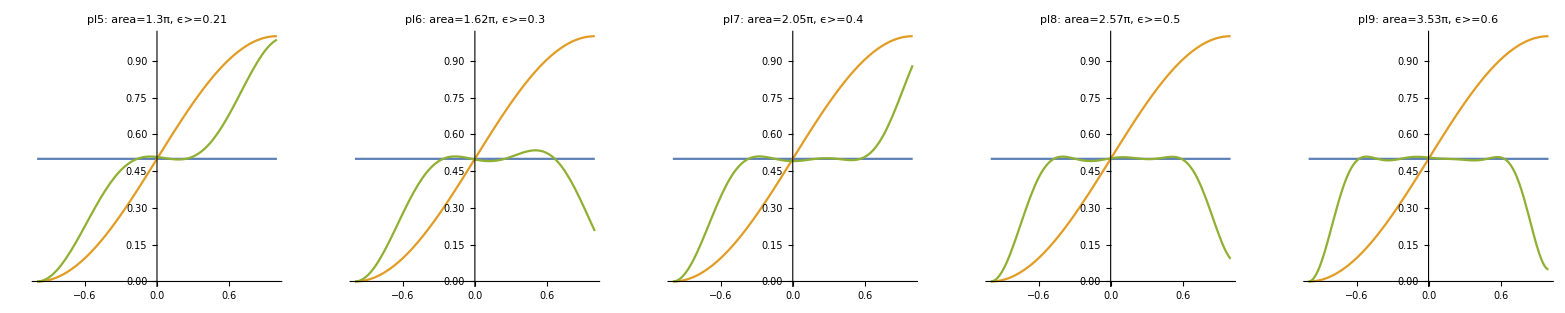

BB5 p=1/3, error=0.01

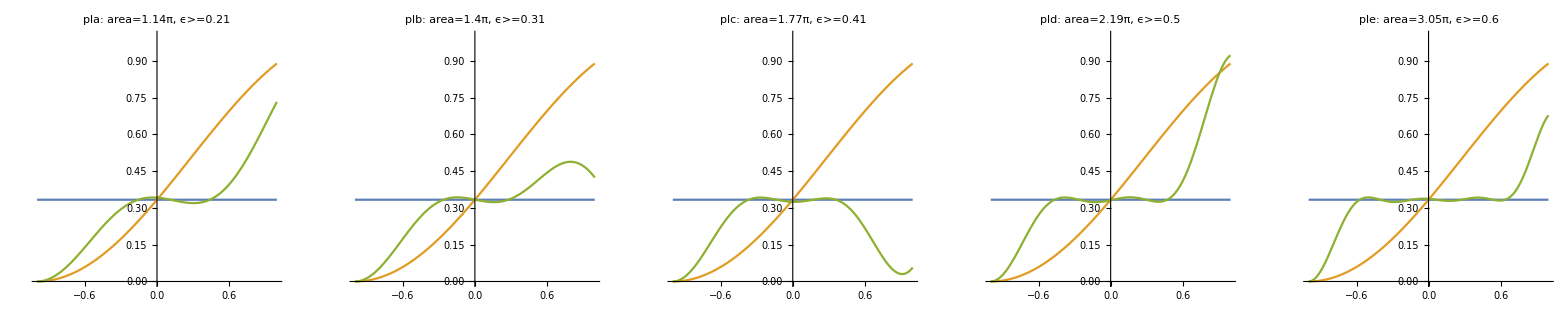

```mathematica
(*N=5*)
sequence=U[Δ5,Ω5].U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl0=plt[1,{Δ1->-0.1498,Δ2->-0.5991,Δ3->0.061,Δ4->0.1052,Δ5->0.53,Ω1->0.1226,Ω2->0.6146,Ω3->0.2228,Ω4->0.2035,Ω5->0.5468},"pl0"];
pl1=plt[1,{Δ1->0.493,Δ2->0.2658,Δ3->-0.0751,Δ4->-0.7437,Δ5->0.9174,Ω1->0.3875,Ω2->0.2595,Ω3->0.9277,Ω4->0.5146,Ω5->0.0008},"pl1"];
pl2=plt[1,{Δ1->0.0943,Δ2->0.7954,Δ3->-0.7931,Δ4->-0.065,Δ5->0.0835,Ω1->0.6801,Ω2->0.6112,Ω3->0.5801,Ω4->0.3356,Ω5->0.3919},"pl2"];
pl3=plt[1,{Δ1->-0.0545,Δ2->1.4828,Δ3->-0.387,Δ4->0.2453,Δ5->0.8319,Ω1->0.3478,Ω2->0.0068,Ω3->1.3012,Ω4->1.2065,Ω5->0.5414},"pl3"];
pl4=plt[1,{Δ1->0.7153,Δ2->-1.0618,Δ3->0.9689,Δ4->-0.0247,Δ5->-0.7218,Ω1->0.6352,Ω2->1.5515,Ω3->1.3354,Ω4->0.3827,Ω5->0.5055},"pl4"];

pl5=plt[1/2,{Δ1->-0.1105,Δ2->0.1518,Δ3->0.3459,Δ4->0.2704,Δ5->-0.022,Ω1->0.5008,Ω2->0.3044,Ω3->0.1134,Ω4->0.2049,Ω5->0.1725},"pl5"];
pl6=plt[1/2,{Δ1->0.1762,Δ2->-0.5907,Δ3->0.317,Δ4->0.3075,Δ5->0.482,Ω1->0.0648,Ω2->0.7113,Ω3->0.0572,Ω4->0.1423,Ω5->0.6477},"pl6"];
pl7=plt[1/2,{Δ1->0.9669,Δ2->0.1908,Δ3->0.3918,Δ4->-0.2729,Δ5->-0.223,Ω1->0.4647,Ω2->0.4313,Ω3->0.887,Ω4->0.2554,Ω5->0.0103},"pl7"];
pl8=plt[1/2,{Δ1->-0.0398,Δ2->0.7624,Δ3->0.6234,Δ4->0.0985,Δ5->0.1008,Ω1->0.1194,Ω2->0.2672,Ω3->1.1019,Ω4->0.8832,Ω5->0.196},"pl8"];
pl9=plt[1/2,{Δ1->0.9048,Δ2->0.2911,Δ3->0.6988,Δ4->-0.2657,Δ5->-0.7036,Ω1->0.4439,Ω2->0.8921,Ω3->1.3299,Ω4->0.0855,Ω5->0.7779},"pl9"];

pla=plt[1/3,{Δ1->0.2225,Δ2->-0.0016,Δ3->0.4223,Δ4->0.1608,Δ5->0.2474,Ω1->0.6386,Ω2->0.0072,Ω3->0.2005,Ω4->0.1105,Ω5->0.1845},"pla"];
plb=plt[1/3,{Δ1->0.0415,Δ2->0.2961,Δ3->0.1176,Δ4->0.4323,Δ5->0.4497,Ω1->0.0345,Ω2->0.4554,Ω3->0.4271,Ω4->0.2026,Ω5->0.2764},"plb"];
plc=plt[1/3,{Δ1->0.5876,Δ2->0.4925,Δ3->-0.0722,Δ4->0.1851,Δ5->0.2926,Ω1->0.3682,Ω2->0.334,Ω3->0.448,Ω4->0.1913,Ω5->0.4326},"plc"];
pld=plt[1/3,{Δ1->-0.0139,Δ2->0.5252,Δ3->-0.1334,Δ4->-0.013,Δ5->1.0914,Ω1->0.5421,Ω2->0.6722,Ω3->0.0148,Ω4->0.288,Ω5->0.6751},"pld"];
ple=plt[1/3,{Δ1->1.2201,Δ2->1.6943,Δ3->0.4905,Δ4->0.6388,Δ5->0.968,Ω1->0.0016,Ω2->0.0305,Ω3->1.6586,Ω4->0.9545,Ω5->0.4021},"ple"];

GGrid[Text[Style["BB5 p=1"<> error,FontSize->20]],{{pl0,pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8,pl9}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/3"<> error,FontSize->20]],{{pla,plb,plc,pld,ple}},ImageSize->Full]
```